```mathematica
Quit[];
```

## Load the package

```mathematica
<<TRQS`
```

Package TRQS version 0.1.1 (last modification: July 21, 2011).

## Integer numbers

```mathematica
?TrueRandomInteger
```

TrueRandomInteger[{i_min,i_max}] returns a random integer in the range [i_min,i_max].
TrueRandomInteger[i] returns a random integer in the range [0,i].
TrueRandomInteger[] returns 0 or 1.

```mathematica
{TrueRandomInteger[],TrueRandomInteger[10],TrueRandomInteger[{10,20}]}
```

{0,5,14}

## Real numbers

```mathematica
?TrueRandomReal
```

TrueRandomReal[{x_min,x_max}] returns a random double in the range [x_min,x_max].
TrueRandomReal[i] returns a random double in the range [0,x].
TrueRandomReal[] returns a random double in the range [0,1].

```mathematica
{TrueRandomReal[],TrueRandomReal[10],TrueRandomReal[{10,20}]}
```

{0.949586,6.83901,17.1675}

## Normal distribution

```mathematica
?TrueRandomRealNormal
```

TrueRandomRealNormal[m,s,dims] provides a sample of random numbers distributed according to the normal distribution N[m,s] in an array of dimensions given by dims.

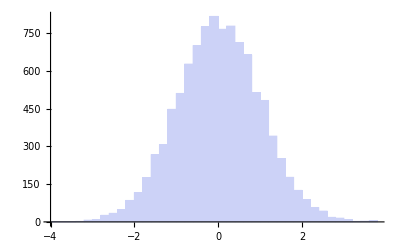

```mathematica
Histogram[Flatten[TrueRandomRealNormal[0,1,{10000}]]]
```

## Ginibre matrix

```mathematica
?TrueGinibreMatrix
```

TrueGinibreMatrix[n] returns n-dimesional complex matrix with entries having real and complex part distributed according to the normal distribution N[0,1].

```mathematica
TrueGinibreMatrix[10,10]
```

{{-0.119776-0.960878 ⅈ,0.332865-0.841497 ⅈ,0.775732+0.0850484 ⅈ,-1.04187+0.783991 ⅈ,0.271095+0.673569 ⅈ,-0.941879-0.636277 ⅈ,-1.27303+0.1313 ⅈ,-0.691737-2.01048 ⅈ,-3.41229-2.11663 ⅈ,-1.7754+1.12839 ⅈ},{0.729082-0.215677 ⅈ,-0.924876+1.04976 ⅈ,0.0383998-1.04253 ⅈ,-0.0905542+0.28307 ⅈ,1.06412-0.998403 ⅈ,2.03806-0.545414 ⅈ,-1.04771-0.350103 ⅈ,0.618991+1.21301 ⅈ,0.269657+0.123327 ⅈ,-1.67135+0.786671 ⅈ},{0.63446+0.0522746 ⅈ,0.904012+0.0455177 ⅈ,-0.373989+0.244316 ⅈ,-0.726178+0.148413 ⅈ,-2.20704+0.1119 ⅈ,0.714966-1.72041 ⅈ,-1.10234+0.13339 ⅈ,0.0397428-0.828711 ⅈ,-0.243443-0.763903 ⅈ,0.889043-1.05952 ⅈ},{-0.810559-0.640616 ⅈ,-0.216704-0.244694 ⅈ,0.123791+1.14036 ⅈ,0.206736-0.430073 ⅈ,0.251654-0.559355 ⅈ,1.0454-1.16109 ⅈ,-0.489061-0.866181 ⅈ,-0.437413+0.969246 ⅈ,-0.336732+0.313628 ⅈ,-1.93004+0.565968 ⅈ},{-1.73303+0.0549465 ⅈ,1.68214+0.403744 ⅈ,2.50942-0.6365 ⅈ,1.32285+0.745208 ⅈ,-0.921116-0.933317 ⅈ,0.000679467+0.722436 ⅈ,1.93548+1.82835 ⅈ,1.24717+0.0981916 ⅈ,-1.71927-0.218562 ⅈ,0.649998+2.29998 ⅈ},{1.43871-0.865631 ⅈ,0.512198+1.06529 ⅈ,-0.744172+0.858885 ⅈ,-0.690755-0.354175 ⅈ,-0.748001+0.0559533 ⅈ,0.0804187+1.09573 ⅈ,1.64282-1.68296 ⅈ,-0.569269+0.545587 ⅈ,0.497161-0.454611 ⅈ,0.353784-0.160274 ⅈ},{0.678537-1.04913 ⅈ,-0.649463+0.259243 ⅈ,-0.497623+0.277562 ⅈ,-0.749406+0.590291 ⅈ,1.00369-0.676675 ⅈ,0.680052+0.0268219 ⅈ,0.53369-0.752582 ⅈ,0.910252-0.349212 ⅈ,-1.31419-0.84614 ⅈ,0.69891-0.931508 ⅈ},{0.571812+1.45317 ⅈ,-0.974742+0.787122 ⅈ,-0.898758-0.368907 ⅈ,0.292583-0.871318 ⅈ,0.489791+1.66329 ⅈ,0.268364+0.312379 ⅈ,-0.325529-0.315735 ⅈ,-1.1367+0.172951 ⅈ,1.13589+2.34543 ⅈ,0.708216+1.1997 ⅈ},{0.98308+1.30776 ⅈ,0.682439+1.45634 ⅈ,0.326676-0.579717 ⅈ,0.136142-0.453683 ⅈ,-0.760635-0.174409 ⅈ,-0.0690529-0.924967 ⅈ,-1.13168+0.255884 ⅈ,0.00443443+0.04209 ⅈ,-0.61807-0.036891 ⅈ,-0.54851-0.295077 ⅈ},{1.02311-0.711109 ⅈ,1.54851-0.137204 ⅈ,0.653148+0.343596 ⅈ,-0.0284483-0.0422907 ⅈ,-1.9037+2.94854 ⅈ,0.821441-1.06752 ⅈ,-0.100727-0.527596 ⅈ,0.327871-1.43154 ⅈ,-0.777737+0.64182 ⅈ,-1.34614+1.24776 ⅈ}}

## Random states - HS measure

```mathematica
statesHS=Table[TrueRandomStateHS[4],{2000}];
```

```mathematica
sortedEvalsHS=Map[Sort[#]&,Map[Chop[Eigenvalues[#]]&,statesHS]]ᵀ;
```

```mathematica
masterplotHS=Histogram[{sortedEvalsHS[[1]],sortedEvalsHS[[2]],sortedEvalsHS[[3]],sortedEvalsHS[[4]]},{0.005},"ProbabilityDensity",PlotRange->{{0,1},{0,61}},ChartBaseStyle->EdgeForm[None],ChartStyle->{Gray,Darker[Gray],LightGray,Darker[LightGray]},
AxesLabel->{"λ","P(λ)"},ImageSize->Large,LabelStyle-> 15];
```

```mathematica
SetDirectory[ToString[NotebookDirectory[]]<>"/plots"];
```

```mathematica
Export["lambda-prob-hs-trqs.pdf",masterplotHS];
Run[" pdf2ps  -dLanguageLevel=3 lambda-prob-hs-trqs.pdf lambda-prob-hs-trqs.eps"];
```

## Random states - Bures measure

```mathematica
statesBures=Table[TrueRandomStateBures[4],{1000}];
```

```mathematica
sortedEvalsBures=Map[Sort[#]&,Map[Chop[Eigenvalues[#]]&,statesBures]]ᵀ;
```

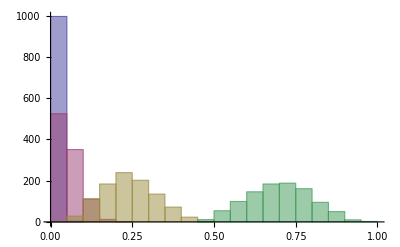

```mathematica
Histogram[{sortedEvalsBures[[1]],sortedEvalsBures[[2]],sortedEvalsBures[[3]],sortedEvalsBures[[4]]}]
```

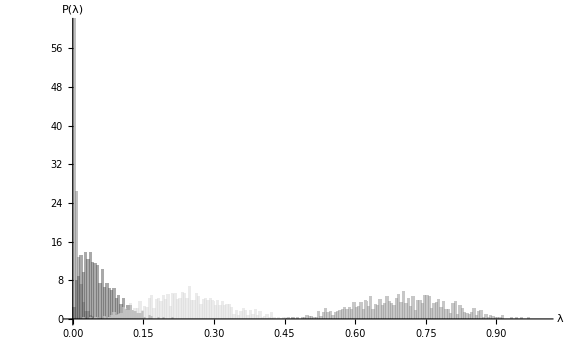

```mathematica
masterplotBures=Histogram[{sortedEvalsBures[[1]],sortedEvalsBures[[2]],sortedEvalsBures[[3]],sortedEvalsBures[[4]]},{0.005},"ProbabilityDensity",PlotRange->{{0,1},{0,61}},ChartBaseStyle->EdgeForm[None],ChartStyle->{Gray,Darker[Gray],LightGray,Darker[LightGray]},
AxesLabel->{"λ","P(λ)"},ImageSize->Large,LabelStyle-> 15]
```

```mathematica
SetDirectory[ToString[NotebookDirectory[]]<>"/plots"];
```

```mathematica
Export["lambda-prob-bures-trqs.pdf",masterplotBures];
Run[" pdf2ps  -dLanguageLevel=3 lambda-prob-bures-trqs.pdf lambda-prob-bures-trqs.eps"];
```

## libQuantis configuration

```mathematica
QuantisGetLibVersion[]
```

2.5

```mathematica
QuantisGetSerialNumber[]
```

080259A410